# Rapport inlämningsuppgift 2

Thomas Gustafsson, TIEDB, thomg@kth.se
Muttakin Karim, TIEDB, muttakin@kth.se

Uppgift 1: Visualisera data

## Sammanfattning

### Uppgift

Nedan finns data för länders total territoriella CO_2-utsläpp och CO_2 per capita. Första listan innehåller länderna. Kombinera länder med data (de är i samma ordning) och visualisera detta med lämpliga grafer som visar utsläpp totalt för de länder som släpper ut mest jämfört med resten av världen. På samma sätt för per capita data. Varje graf skall ha följande:
1. Axelbeckningar
2. Enheter
3. Figurtext som kortfattat förklarar figuren

#### länder

```mathematica
countries={"Africa Eastern and Southern","Afghanistan","Africa Western and Central","Angola","Albania","Andorra","Arab World","United Arab Emirates","Argentina","Armenia","Antigua and Barbuda","Australia","Austria","Azerbaijan","Burundi","Belgium","Benin","Burkina Faso","Bangladesh","Bulgaria","Bahrain","Bahamas, The","Bosnia and Herzegovina","Belarus","Belize","Bolivia","Brazil","Barbados","Brunei Darussalam","Bhutan","Botswana","Central African Republic","Canada","Central Europe and the Baltics","Switzerland","Chile","China","Cote d'Ivoire","Cameroon","Congo, Dem. Rep.","Congo, Rep.","Colombia","Comoros","Cabo Verde","Costa Rica","Caribbean small states","Cuba","Cyprus","Czech Republic","Germany","Djibouti","Dominica","Denmark","Dominican Republic","Algeria","East Asia & Pacific (excluding high income)","Early-demographic dividend","East Asia & Pacific","Europe & Central Asia (excluding high income)","Europe & Central Asia","Ecuador","Egypt, Arab Rep.","Euro area","Eritrea","Spain","Estonia","Ethiopia","European Union","Fragile and conflict affected situations","Finland","Fiji","France","Micronesia, Fed. Sts.","Gabon","United Kingdom","Georgia","Ghana","Guinea","Gambia, The","Guinea-Bissau","Equatorial Guinea","Greece","Grenada","Guatemala","Guyana","High income","Honduras","Heavily indebted poor countries (HIPC)","Croatia","Haiti","Hungary","IBRD only","IDA & IBRD total","IDA total","IDA blend","Indonesia","IDA only","India","Ireland","Iran, Islamic Rep.","Iraq","Iceland","Israel","Italy","Jamaica","Jordan","Japan","Kazakhstan","Kenya","Kyrgyz Republic","Cambodia","Kiribati","St. Kitts and Nevis","Korea, Rep.","Kuwait","Latin America & Caribbean (excluding high income)","Lao PDR","Lebanon","Liberia","Libya","St. Lucia","Latin America & Caribbean","Least developed countries: UN classification","Low income","Liechtenstein","Sri Lanka","Lower middle income","Low & middle income","Lesotho","Late-demographic dividend","Lithuania","Luxembourg","Latvia","Morocco","Moldova","Madagascar","Maldives","Middle East & North Africa","Mexico","Marshall Islands","Middle income","North Macedonia","Mali","Malta","Myanmar","Middle East & North Africa (excluding high income)","Montenegro","Mongolia","Mozambique","Mauritania","Mauritius","Malawi","Malaysia","North America","Namibia","Niger","Nigeria","Nicaragua","Netherlands","Norway","Nepal","Nauru","New Zealand","OECD members","Oman","Other small states","Pakistan","Panama","Peru","Philippines","Palau","Papua New Guinea","Poland","Pre-demographic dividend","Korea, Dem. People's Rep.","Portugal","Paraguay","Pacific island small states","Post-demographic dividend","Qatar","Romania","Russian Federation","Rwanda","South Asia","Saudi Arabia","Sudan","Senegal","Singapore","Solomon Islands","Sierra Leone","El Salvador","Somalia","Serbia","Sub-Saharan Africa (excluding high income)","South Sudan","Sub-Saharan Africa","Small states","Sao Tome and Principe","Suriname","Slovak Republic","Slovenia","Sweden","Eswatini","Seychelles","Syrian Arab Republic","Chad","East Asia & Pacific (IDA & IBRD countries)","Europe & Central Asia (IDA & IBRD countries)","Togo","Thailand","Tajikistan","Turkmenistan","Latin America & the Caribbean (IDA & IBRD countries)","Timor-Leste","Middle East & North Africa (IDA & IBRD countries)","Tonga","South Asia (IDA & IBRD)","Sub-Saharan Africa (IDA & IBRD countries)","Trinidad and Tobago","Tunisia","Turkey","Tuvalu","Tanzania","Uganda","Ukraine","Upper middle income","Uruguay","United States","Uzbekistan","St. Vincent and the Grenadines","Venezuela, RB","Vietnam","Vanuatu","World","Samoa","Yemen, Rep.","South Africa","Zambia","Zimbabwe"};
```

#### CO_2 utsläpp per capita (ton)

```mathematica
co2perCapita={0.933541201,0.200151071,0.515544239,0.887380364,1.939731563,5.97340536,4.438715965,20.7974984,3.987234198,1.880246268,5.504663385,15.47551649,7.146637625,3.221402183,0.05279463,8.179711061,0.688722324,0.216186485,0.512837314,5.854773434,19.59297584,5.86046391,6.781131607,6.2540208,1.775127848,2.000327663,2.041874199,4.360870779,16.64490862,1.829277992,3.64230522,0.070718706,15.49702527,6.597232486,4.401991044,4.624872245,7.405211347,0.395305384,0.341842908,0.026169263,0.613992586,1.600650618,0.312379103,1.140200528,1.652184053,5.017034408,2.202300094,6.079400502,9.640704998,8.558389812,0.510989933,2.513053919,5.761494164,2.363757648,3.591657418,5.720397083,2.27814572,6.361179651,7.07331348,6.690105957,2.3138123,2.502042142,6.454837567,0.231696216,5.5203504,12.103085,0.149050931,6.424038741,0.868444604,8.04275205,2.150561976,4.619241205,1.598011364,2.175272204,5.398708138,2.538541691,0.541201382,0.251323233,0.249989913,0.165394728,5.095625096,6.08317505,2.691814193,1.113969273,3.13219265,10.25453315,1.019032757,0.271687567,4.055928762,0.299374738,4.745506244,4.382903441,3.40988701,0.560235135,0.920386827,2.178461553,0.37549488,1.799825446,7.624325193,7.693012599,4.895195361,6.237224322,6.976403837,5.376374339,2.899634155,2.478595273,8.74225771,12.06196914,0.358028408,1.73973556,0.686777895,0.690595812,4.958236393,12.22459136,21.62272431,2.413939907,2.660908493,4.039707217,0.273917114,8.825249137,2.14415306,2.637362569,0.335389683,0.23673353,3.692177857,0.99815413,1.730955497,3.355676738,1.218975994,6.518254124,4.137005929,15.33020808,3.959165078,1.850726784,3.171832063,0.128320761,3.703674976,5.638657141,3.741477725,3.252756283,3.69823452,3.538239148,0.294583928,3.198316241,0.605492803,3.841040725,4.049968902,6.725098053,0.225115201,0.908407126,3.264040313,0.086533726,7.600220413,15.27087561,1.735898378,0.102037038,0.667110199,0.805815233,8.772823734,7.031361189,0.428179218,6.555534744,6.572664572,8.835263958,15.19212436,6.406682315,0.981820105,2.42765632,1.69681923,1.33369096,16.19116744,0.866804457,8.235472255,0.557925928,0.709208588,4.840612761,1.210453778,1.539504166,9.853587312,32.41563917,3.845132759,11.12661837,0.087790824,1.526651238,15.26878053,0.483235878,0.621912357,8.399134832,0.566740598,0.133330736,1.060625411,0.04597479,6.521922194,0.763112676,0.125729734,0.763618494,5.859845144,0.663406498,3.611192614,6.058635474,6.774695332,3.538009127,0.959275668,6.407474008,1.647087511,0.069131598,5.782778671,7.141751179,0.286471389,3.714039204,0.80541954,12.25964817,2.614462991,0.504741813,3.861347119,1.841103111,1.526651238,0.763618494,12.77844012,2.592258865,5.01541837,0.86918731,0.205634733,0.143462178,4.154180631,6.261836804,1.890244079,15.24087458,3.401191282,2.540604301,4.782754887,2.698805922,0.615016657,4.483523912,1.631587535,0.326681763,7.496644895,0.446065443,0.849792905};
```

#### territoriella CO_2 utsläpp (kton)

```mathematica
co2emissions={600351.1333,7440,224380,27340,5560,460,1863603.727,200300,177410,5550,530,386620,63180,32020,590,93470,7910,4270,82760,41130,30750,2260,22540,59310,680,22710,427710,1250,7140,1380,8210,330,574400,676470,37480,86620,10313460,9910,8620,2200,3220,79490,260,620,8260,36920,24970,7230,102480,709540,490,180,33380,25120,151670,11907866.46,7400359.524,14810056.87,2949087.39,6142069.263,39530,246260,2207420,800,258340,16000,16280,2871000,771602.9297,44360,1900,309960,180,4610,358800,9460,16110,3120,570,310,6670,65290,300,18210,2440,12366368.33,9770,211980,16580,3330,46390,20938730,21860535.52,915178.5696,505410,583110,407199.3144,2434520,37110,629290,188140,2200,61970,324850,8510,24700,1106150,220450,18400,11000,11160,80,260,630870,89460,1408370,18790,27710,1320,58940,390,1689187.436,338640.0291,149413.7119,140,21630,5608350.968,21334207.73,2570,14912796.92,11590,9320,7630,66680,8590,3370,1910,2531611.759,472140,190,21177938.67,7370,5620,1550,32520,1470946.392,2520,21320,6640,4000,4130,1570,239620,5558099.304,4250,2290,130670,5210,151170,37350,12030,70,32210,11998460,73370,197072.5527,208370,10140,54280,142240,290,7460,312740,513004.5719,18120,49780,8420,3780,10935463.93,90170,74880,1607550,1080,2770040,514600,20200,9860,47360,370,1020,6810,690,45540,822805.4476,1380,823424.7218,237761.658,140,2080,33000,14050,36000,1090,620,27910,1070,11889820,3278021.798,2260,257860,7330,71730,1633250,640,1461080,190,2770040,823424.7218,17760,29980,412970,10,11580,6130,185370,15569855.45,6520,4981300,112090,280,138160,257860,180,34041045.97,320,9310,433250,7740,12270};
```

### Resultat

Gruppen använde List[ ] funktionen för att föra samman tre tabeller till två listor som visade världens länder och regioners koldioxidutsläpp per capita och totala antal utsläpp av dessa. Select[ ] för att filtrera data och få fram de länder med högst utsläpp, sedan skriva ut dessa i BarChart grafer.

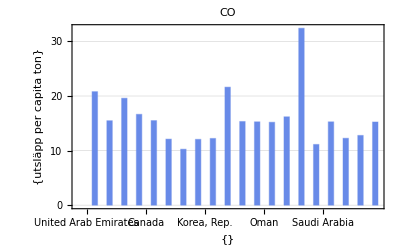

Om man ser grafen för territoriella koldioxidutsläpp i kiloton är det tydligt att USA:s utsläpp är nästan lika stora som världens “lower & middle income” länder totalt. Tyskland har lika stora utsläpp som Subsahariska Afrika. Utsläppen av USA står även för över en sjundedel för hela världens utsläpp totalt.

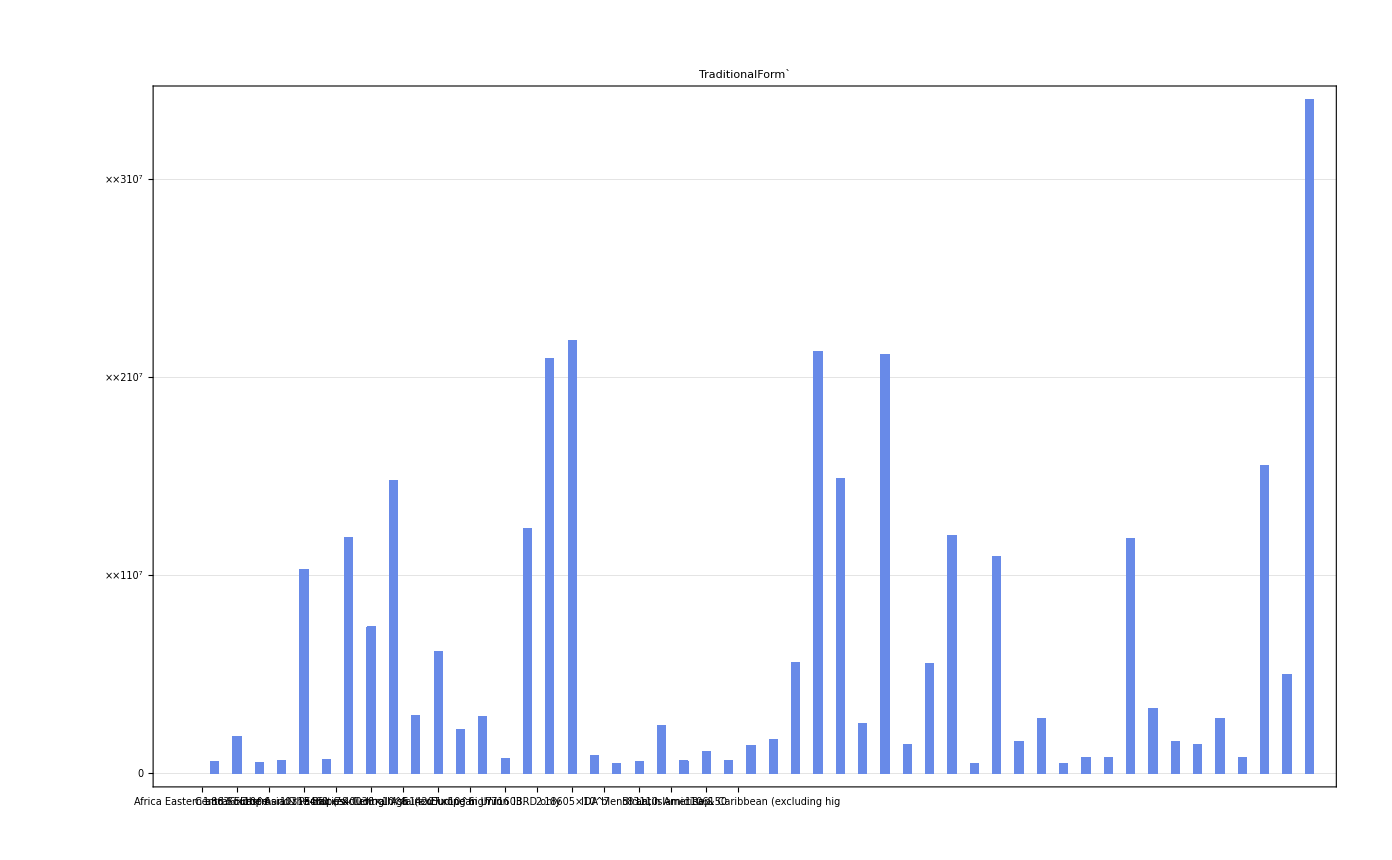

## Visualisera data

### Listor för utsläpp per capita och territoriala utsläpp

Sammanställning av uppgiftens data.

countries={"Africa Eastern and Southern","Afghanistan","Africa Western and Central","Angola","Albania","Andorra","Arab World","United Arab Emirates","Argentina","Armenia","Antigua and Barbuda","Australia","Austria","Azerbaijan","Burundi","Belgium","Benin","Burkina Faso","Bangladesh","Bulgaria","Bahrain","Bahamas, The","Bosnia and Herzegovina","Belarus","Belize","Bolivia","Brazil","Barbados","Brunei Darussalam","Bhutan","Botswana","Central African Republic","Canada","Central Europe and the Baltics","Switzerland","Chile","China","Cote d'Ivoire","Cameroon","Congo, Dem. Rep.","Congo, Rep.","Colombia","Comoros","Cabo Verde","Costa Rica","Caribbean small states","Cuba","Cyprus","Czech Republic","Germany","Djibouti","Dominica","Denmark","Dominican Republic","Algeria","East Asia & Pacific (excluding high income)","Early-demographic dividend","East Asia & Pacific","Europe & Central Asia (excluding high income)","Europe & Central Asia","Ecuador","Egypt, Arab Rep.","Euro area","Eritrea","Spain","Estonia","Ethiopia","European Union","Fragile and conflict affected situations","Finland","Fiji","France","Micronesia, Fed. Sts.","Gabon","United Kingdom","Georgia","Ghana","Guinea","Gambia, The","Guinea-Bissau","Equatorial Guinea","Greece","Grenada","Guatemala","Guyana","High income","Honduras","Heavily indebted poor countries (HIPC)","Croatia","Haiti","Hungary","IBRD only","IDA & IBRD total","IDA total","IDA blend","Indonesia","IDA only","India","Ireland","Iran, Islamic Rep.","Iraq","Iceland","Israel","Italy","Jamaica","Jordan","Japan","Kazakhstan","Kenya","Kyrgyz Republic","Cambodia","Kiribati","St. Kitts and Nevis","Korea, Rep.","Kuwait","Latin America & Caribbean (excluding high income)","Lao PDR","Lebanon","Liberia","Libya","St. Lucia","Latin America & Caribbean","Least developed countries: UN classification","Low income","Liechtenstein","Sri Lanka","Lower middle income","Low & middle income","Lesotho","Late-demographic dividend","Lithuania","Luxembourg","Latvia","Morocco","Moldova","Madagascar","Maldives","Middle East & North Africa","Mexico","Marshall Islands","Middle income","North Macedonia","Mali","Malta","Myanmar","Middle East & North Africa (excluding high income)","Montenegro","Mongolia","Mozambique","Mauritania","Mauritius","Malawi","Malaysia","North America","Namibia","Niger","Nigeria","Nicaragua","Netherlands","Norway","Nepal","Nauru","New Zealand","OECD members","Oman","Other small states","Pakistan","Panama","Peru","Philippines","Palau","Papua New Guinea","Poland","Pre-demographic dividend","Korea, Dem. People's Rep.","Portugal","Paraguay","Pacific island small states","Post-demographic dividend","Qatar","Romania","Russian Federation","Rwanda","South Asia","Saudi Arabia","Sudan","Senegal","Singapore","Solomon Islands","Sierra Leone","El Salvador","Somalia","Serbia","Sub-Saharan Africa (excluding high income)","South Sudan","Sub-Saharan Africa","Small states","Sao Tome and Principe","Suriname","Slovak Republic","Slovenia","Sweden","Eswatini","Seychelles","Syrian Arab Republic","Chad","East Asia & Pacific (IDA & IBRD countries)","Europe & Central Asia (IDA & IBRD countries)","Togo","Thailand","Tajikistan","Turkmenistan","Latin America & the Caribbean (IDA & IBRD countries)","Timor-Leste","Middle East & North Africa (IDA & IBRD countries)","Tonga","South Asia (IDA & IBRD)","Sub-Saharan Africa (IDA & IBRD countries)","Trinidad and Tobago","Tunisia","Turkey","Tuvalu","Tanzania","Uganda","Ukraine","Upper middle income","Uruguay","United States","Uzbekistan","St. Vincent and the Grenadines","Venezuela, RB","Vietnam","Vanuatu","World","Samoa","Yemen, Rep.","South Africa","Zambia","Zimbabwe"};

```mathematica
co2perCapita={0.933541201,0.200151071,0.515544239,0.887380364,1.939731563,5.97340536,4.438715965,20.7974984,3.987234198,1.880246268,5.504663385,15.47551649,7.146637625,3.221402183,0.05279463,8.179711061,0.688722324,0.216186485,0.512837314,5.854773434,19.59297584,5.86046391,6.781131607,6.2540208,1.775127848,2.000327663,2.041874199,4.360870779,16.64490862,1.829277992,3.64230522,0.070718706,15.49702527,6.597232486,4.401991044,4.624872245,7.405211347,0.395305384,0.341842908,0.026169263,0.613992586,1.600650618,0.312379103,1.140200528,1.652184053,5.017034408,2.202300094,6.079400502,9.640704998,8.558389812,0.510989933,2.513053919,5.761494164,2.363757648,3.591657418,5.720397083,2.27814572,6.361179651,7.07331348,6.690105957,2.3138123,2.502042142,6.454837567,0.231696216,5.5203504,12.103085,0.149050931,6.424038741,0.868444604,8.04275205,2.150561976,4.619241205,1.598011364,2.175272204,5.398708138,2.538541691,0.541201382,0.251323233,0.249989913,0.165394728,5.095625096,6.08317505,2.691814193,1.113969273,3.13219265,10.25453315,1.019032757,0.271687567,4.055928762,0.299374738,4.745506244,4.382903441,3.40988701,0.560235135,0.920386827,2.178461553,0.37549488,1.799825446,7.624325193,7.693012599,4.895195361,6.237224322,6.976403837,5.376374339,2.899634155,2.478595273,8.74225771,12.06196914,0.358028408,1.73973556,0.686777895,0.690595812,4.958236393,12.22459136,21.62272431,2.413939907,2.660908493,4.039707217,0.273917114,8.825249137,2.14415306,2.637362569,0.335389683,0.23673353,3.692177857,0.99815413,1.730955497,3.355676738,1.218975994,6.518254124,4.137005929,15.33020808,3.959165078,1.850726784,3.171832063,0.128320761,3.703674976,5.638657141,3.741477725,3.252756283,3.69823452,3.538239148,0.294583928,3.198316241,0.605492803,3.841040725,4.049968902,6.725098053,0.225115201,0.908407126,3.264040313,0.086533726,7.600220413,15.27087561,1.735898378,0.102037038,0.667110199,0.805815233,8.772823734,7.031361189,0.428179218,6.555534744,6.572664572,8.835263958,15.19212436,6.406682315,0.981820105,2.42765632,1.69681923,1.33369096,16.19116744,0.866804457,8.235472255,0.557925928,0.709208588,4.840612761,1.210453778,1.539504166,9.853587312,32.41563917,3.845132759,11.12661837,0.087790824,1.526651238,15.26878053,0.483235878,0.621912357,8.399134832,0.566740598,0.133330736,1.060625411,0.04597479,6.521922194,0.763112676,0.125729734,0.763618494,5.859845144,0.663406498,3.611192614,6.058635474,6.774695332,3.538009127,0.959275668,6.407474008,1.647087511,0.069131598,5.782778671,7.141751179,0.286471389,3.714039204,0.80541954,12.25964817,2.614462991,0.504741813,3.861347119,1.841103111,1.526651238,0.763618494,12.77844012,2.592258865,5.01541837,0.86918731,0.205634733,0.143462178,4.154180631,6.261836804,1.890244079,15.24087458,3.401191282,2.540604301,4.782754887,2.698805922,0.615016657,4.483523912,1.631587535,0.326681763,7.496644895,0.446065443,0.849792905};
```

```mathematica
co2emissions={600351.1333,7440,224380,27340,5560,460,1863603.727,200300,177410,5550,530,386620,63180,32020,590,93470,7910,4270,82760,41130,30750,2260,22540,59310,680,22710,427710,1250,7140,1380,8210,330,574400,676470,37480,86620,10313460,9910,8620,2200,3220,79490,260,620,8260,36920,24970,7230,102480,709540,490,180,33380,25120,151670,11907866.46,7400359.524,14810056.87,2949087.39,6142069.263,39530,246260,2207420,800,258340,16000,16280,2871000,771602.9297,44360,1900,309960,180,4610,358800,9460,16110,3120,570,310,6670,65290,300,18210,2440,12366368.33,9770,211980,16580,3330,46390,20938730,21860535.52,915178.5696,505410,583110,407199.3144,2434520,37110,629290,188140,2200,61970,324850,8510,24700,1106150,220450,18400,11000,11160,80,260,630870,89460,1408370,18790,27710,1320,58940,390,1689187.436,338640.0291,149413.7119,140,21630,5608350.968,21334207.73,2570,14912796.92,11590,9320,7630,66680,8590,3370,1910,2531611.759,472140,190,21177938.67,7370,5620,1550,32520,1470946.392,2520,21320,6640,4000,4130,1570,239620,5558099.304,4250,2290,130670,5210,151170,37350,12030,70,32210,11998460,73370,197072.5527,208370,10140,54280,142240,290,7460,312740,513004.5719,18120,49780,8420,3780,10935463.93,90170,74880,1607550,1080,2770040,514600,20200,9860,47360,370,1020,6810,690,45540,822805.4476,1380,823424.7218,237761.658,140,2080,33000,14050,36000,1090,620,27910,1070,11889820,3278021.798,2260,257860,7330,71730,1633250,640,1461080,190,2770040,823424.7218,17760,29980,412970,10,11580,6130,185370,15569855.45,6520,4981300,112090,280,138160,257860,180,34041045.97,320,9310,433250,7740,12270};
```

Skapa första listan som för samman länder och koldioxid per capita.

```mathematica
list=Table[{countries⟦i⟧,co2perCapita⟦i⟧},{i,1,Length[co2perCapita]}]
```

{{Africa Eastern and Southern,0.933541},{Afghanistan,0.200151},{Africa Western and Central,0.515544},{Angola,0.88738},{Albania,1.93973},{Andorra,5.97341},{Arab World,4.43872},{United Arab Emirates,20.7975},{Argentina,3.98723},{Armenia,1.88025},{Antigua and Barbuda,5.50466},{Australia,15.4755},{Austria,7.14664},{Azerbaijan,3.2214},{Burundi,0.0527946},{Belgium,8.17971},{Benin,0.688722},{Burkina Faso,0.216186},{Bangladesh,0.512837},{Bulgaria,5.85477},{Bahrain,19.593},{Bahamas, The,5.86046},{Bosnia and Herzegovina,6.78113},{Belarus,6.25402},{Belize,1.77513},{Bolivia,2.00033},{Brazil,2.04187},{Barbados,4.36087},{Brunei Darussalam,16.6449},{Bhutan,1.82928},{Botswana,3.64231},{Central African Republic,0.0707187},{Canada,15.497},{Central Europe and the Baltics,6.59723},{Switzerland,4.40199},{Chile,4.62487},{China,7.40521},{Cote d'Ivoire,0.395305},{Cameroon,0.341843},{Congo, Dem. Rep.,0.0261693},{Congo, Rep.,0.613993},{Colombia,1.60065},{Comoros,0.312379},{Cabo Verde,1.1402},{Costa Rica,1.65218},{Caribbean small states,5.01703},{Cuba,2.2023},{Cyprus,6.0794},{Czech Republic,9.6407},{Germany,8.55839},{Djibouti,0.51099},{Dominica,2.51305},{Denmark,5.76149},{Dominican Republic,2.36376},{Algeria,3.59166},{East Asia & Pacific (excluding high income),5.7204},{Early-demographic dividend,2.27815},{East Asia & Pacific,6.36118},{Europe & Central Asia (excluding high income),7.07331},{Europe & Central Asia,6.69011},{Ecuador,2.31381},{Egypt, Arab Rep.,2.50204},{Euro area,6.45484},{Eritrea,0.231696},{Spain,5.52035},{Estonia,12.1031},{Ethiopia,0.149051},{European Union,6.42404},{Fragile and conflict affected situations,0.868445},{Finland,8.04275},{Fiji,2.15056},{France,4.61924},{Micronesia, Fed. Sts.,1.59801},{Gabon,2.17527},{United Kingdom,5.39871},{Georgia,2.53854},{Ghana,0.541201},{Guinea,0.251323},{Gambia, The,0.24999},{Guinea-Bissau,0.165395},{Equatorial Guinea,5.09563},{Greece,6.08318},{Grenada,2.69181},{Guatemala,1.11397},{Guyana,3.13219},{High income,10.2545},{Honduras,1.01903},{Heavily indebted poor countries (HIPC),0.271688},{Croatia,4.05593},{Haiti,0.299375},{Hungary,4.74551},{IBRD only,4.3829},{IDA & IBRD total,3.40989},{IDA total,0.560235},{IDA blend,0.920387},{Indonesia,2.17846},{IDA only,0.375495},{India,1.79983},{Ireland,7.62433},{Iran, Islamic Rep.,7.69301},{Iraq,4.8952},{Iceland,6.23722},{Israel,6.9764},{Italy,5.37637},{Jamaica,2.89963},{Jordan,2.4786},{Japan,8.74226},{Kazakhstan,12.062},{Kenya,0.358028},{Kyrgyz Republic,1.73974},{Cambodia,0.686778},{Kiribati,0.690596},{St. Kitts and Nevis,4.95824},{Korea, Rep.,12.2246},{Kuwait,21.6227},{Latin America & Caribbean (excluding high income),2.41394},{Lao PDR,2.66091},{Lebanon,4.03971},{Liberia,0.273917},{Libya,8.82525},{St. Lucia,2.14415},{Latin America & Caribbean,2.63736},{Least developed countries: UN classification,0.33539},{Low income,0.236734},{Liechtenstein,3.69218},{Sri Lanka,0.998154},{Lower middle income,1.73096},{Low & middle income,3.35568},{Lesotho,1.21898},{Late-demographic dividend,6.51825},{Lithuania,4.13701},{Luxembourg,15.3302},{Latvia,3.95917},{Morocco,1.85073},{Moldova,3.17183},{Madagascar,0.128321},{Maldives,3.70367},{Middle East & North Africa,5.63866},{Mexico,3.74148},{Marshall Islands,3.25276},{Middle income,3.69823},{North Macedonia,3.53824},{Mali,0.294584},{Malta,3.19832},{Myanmar,0.605493},{Middle East & North Africa (excluding high income),3.84104},{Montenegro,4.04997},{Mongolia,6.7251},{Mozambique,0.225115},{Mauritania,0.908407},{Mauritius,3.26404},{Malawi,0.0865337},{Malaysia,7.60022},{North America,15.2709},{Namibia,1.7359},{Niger,0.102037},{Nigeria,0.66711},{Nicaragua,0.805815},{Netherlands,8.77282},{Norway,7.03136},{Nepal,0.428179},{Nauru,6.55553},{New Zealand,6.57266},{OECD members,8.83526},{Oman,15.1921},{Other small states,6.40668},{Pakistan,0.98182},{Panama,2.42766},{Peru,1.69682},{Philippines,1.33369},{Palau,16.1912},{Papua New Guinea,0.866804},{Poland,8.23547},{Pre-demographic dividend,0.557926},{Korea, Dem. People's Rep.,0.709209},{Portugal,4.84061},{Paraguay,1.21045},{Pacific island small states,1.5395},{Post-demographic dividend,9.85359},{Qatar,32.4156},{Romania,3.84513},{Russian Federation,11.1266},{Rwanda,0.0877908},{South Asia,1.52665},{Saudi Arabia,15.2688},{Sudan,0.483236},{Senegal,0.621912},{Singapore,8.39913},{Solomon Islands,0.566741},{Sierra Leone,0.133331},{El Salvador,1.06063},{Somalia,0.0459748},{Serbia,6.52192},{Sub-Saharan Africa (excluding high income),0.763113},{South Sudan,0.12573},{Sub-Saharan Africa,0.763618},{Small states,5.85985},{Sao Tome and Principe,0.663406},{Suriname,3.61119},{Slovak Republic,6.05864},{Slovenia,6.7747},{Sweden,3.53801},{Eswatini,0.959276},{Seychelles,6.40747},{Syrian Arab Republic,1.64709},{Chad,0.0691316},{East Asia & Pacific (IDA & IBRD countries),5.78278},{Europe & Central Asia (IDA & IBRD countries),7.14175},{Togo,0.286471},{Thailand,3.71404},{Tajikistan,0.80542},{Turkmenistan,12.2596},{Latin America & the Caribbean (IDA & IBRD countries),2.61446},{Timor-Leste,0.504742},{Middle East & North Africa (IDA & IBRD countries),3.86135},{Tonga,1.8411},{South Asia (IDA & IBRD),1.52665},{Sub-Saharan Africa (IDA & IBRD countries),0.763618},{Trinidad and Tobago,12.7784},{Tunisia,2.59226},{Turkey,5.01542},{Tuvalu,0.869187},{Tanzania,0.205635},{Uganda,0.143462},{Ukraine,4.15418},{Upper middle income,6.26184},{Uruguay,1.89024},{United States,15.2409},{Uzbekistan,3.40119},{St. Vincent and the Grenadines,2.5406},{Venezuela, RB,4.78275},{Vietnam,2.69881},{Vanuatu,0.615017},{World,4.48352},{Samoa,1.63159},{Yemen, Rep.,0.326682},{South Africa,7.49664},{Zambia,0.446065},{Zimbabwe,0.849793}}

Skapa lista för att visa de 10 länder som har högst utsläpp av koldioxid per capita.

```mathematica
chart1=Select[list,#⟦2⟧>10&]
```

{{United Arab Emirates,20.7975},{Australia,15.4755},{Bahrain,19.593},{Brunei Darussalam,16.6449},{Canada,15.497},{Estonia,12.1031},{High income,10.2545},{Kazakhstan,12.062},{Korea, Rep.,12.2246},{Kuwait,21.6227},{Luxembourg,15.3302},{North America,15.2709},{Oman,15.1921},{Palau,16.1912},{Qatar,32.4156},{Russian Federation,11.1266},{Saudi Arabia,15.2688},{Turkmenistan,12.2596},{Trinidad and Tobago,12.7784},{United States,15.2409}}

Skapa andra listan som för samman länder och totala koldioxidutsläpp.

```mathematica
list2=Table[{countries⟦i⟧,co2emissions⟦i⟧},{i,1,Length[co2emissions]}]
```

{{Africa Eastern and Southern,600351.},{Afghanistan,7440},{Africa Western and Central,224380},{Angola,27340},{Albania,5560},{Andorra,460},{Arab World,1.8636×10^6},{United Arab Emirates,200300},{Argentina,177410},{Armenia,5550},{Antigua and Barbuda,530},{Australia,386620},{Austria,63180},{Azerbaijan,32020},{Burundi,590},{Belgium,93470},{Benin,7910},{Burkina Faso,4270},{Bangladesh,82760},{Bulgaria,41130},{Bahrain,30750},{Bahamas, The,2260},{Bosnia and Herzegovina,22540},{Belarus,59310},{Belize,680},{Bolivia,22710},{Brazil,427710},{Barbados,1250},{Brunei Darussalam,7140},{Bhutan,1380},{Botswana,8210},{Central African Republic,330},{Canada,574400},{Central Europe and the Baltics,676470},{Switzerland,37480},{Chile,86620},{China,10313460},{Cote d'Ivoire,9910},{Cameroon,8620},{Congo, Dem. Rep.,2200},{Congo, Rep.,3220},{Colombia,79490},{Comoros,260},{Cabo Verde,620},{Costa Rica,8260},{Caribbean small states,36920},{Cuba,24970},{Cyprus,7230},{Czech Republic,102480},{Germany,709540},{Djibouti,490},{Dominica,180},{Denmark,33380},{Dominican Republic,25120},{Algeria,151670},{East Asia & Pacific (excluding high income),1.19079×10^7},{Early-demographic dividend,7.40036×10^6},{East Asia & Pacific,1.48101×10^7},{Europe & Central Asia (excluding high income),2.94909×10^6},{Europe & Central Asia,6.14207×10^6},{Ecuador,39530},{Egypt, Arab Rep.,246260},{Euro area,2207420},{Eritrea,800},{Spain,258340},{Estonia,16000},{Ethiopia,16280},{European Union,2871000},{Fragile and conflict affected situations,771603.},{Finland,44360},{Fiji,1900},{France,309960},{Micronesia, Fed. Sts.,180},{Gabon,4610},{United Kingdom,358800},{Georgia,9460},{Ghana,16110},{Guinea,3120},{Gambia, The,570},{Guinea-Bissau,310},{Equatorial Guinea,6670},{Greece,65290},{Grenada,300},{Guatemala,18210},{Guyana,2440},{High income,1.23664×10^7},{Honduras,9770},{Heavily indebted poor countries (HIPC),211980},{Croatia,16580},{Haiti,3330},{Hungary,46390},{IBRD only,20938730},{IDA & IBRD total,2.18605×10^7},{IDA total,915179.},{IDA blend,505410},{Indonesia,583110},{IDA only,407199.},{India,2434520},{Ireland,37110},{Iran, Islamic Rep.,629290},{Iraq,188140},{Iceland,2200},{Israel,61970},{Italy,324850},{Jamaica,8510},{Jordan,24700},{Japan,1106150},{Kazakhstan,220450},{Kenya,18400},{Kyrgyz Republic,11000},{Cambodia,11160},{Kiribati,80},{St. Kitts and Nevis,260},{Korea, Rep.,630870},{Kuwait,89460},{Latin America & Caribbean (excluding high income),1408370},{Lao PDR,18790},{Lebanon,27710},{Liberia,1320},{Libya,58940},{St. Lucia,390},{Latin America & Caribbean,1.68919×10^6},{Least developed countries: UN classification,338640.},{Low income,149414.},{Liechtenstein,140},{Sri Lanka,21630},{Lower middle income,5.60835×10^6},{Low & middle income,2.13342×10^7},{Lesotho,2570},{Late-demographic dividend,1.49128×10^7},{Lithuania,11590},{Luxembourg,9320},{Latvia,7630},{Morocco,66680},{Moldova,8590},{Madagascar,3370},{Maldives,1910},{Middle East & North Africa,2.53161×10^6},{Mexico,472140},{Marshall Islands,190},{Middle income,2.11779×10^7},{North Macedonia,7370},{Mali,5620},{Malta,1550},{Myanmar,32520},{Middle East & North Africa (excluding high income),1.47095×10^6},{Montenegro,2520},{Mongolia,21320},{Mozambique,6640},{Mauritania,4000},{Mauritius,4130},{Malawi,1570},{Malaysia,239620},{North America,5.5581×10^6},{Namibia,4250},{Niger,2290},{Nigeria,130670},{Nicaragua,5210},{Netherlands,151170},{Norway,37350},{Nepal,12030},{Nauru,70},{New Zealand,32210},{OECD members,11998460},{Oman,73370},{Other small states,197073.},{Pakistan,208370},{Panama,10140},{Peru,54280},{Philippines,142240},{Palau,290},{Papua New Guinea,7460},{Poland,312740},{Pre-demographic dividend,513005.},{Korea, Dem. People's Rep.,18120},{Portugal,49780},{Paraguay,8420},{Pacific island small states,3780},{Post-demographic dividend,1.09355×10^7},{Qatar,90170},{Romania,74880},{Russian Federation,1607550},{Rwanda,1080},{South Asia,2770040},{Saudi Arabia,514600},{Sudan,20200},{Senegal,9860},{Singapore,47360},{Solomon Islands,370},{Sierra Leone,1020},{El Salvador,6810},{Somalia,690},{Serbia,45540},{Sub-Saharan Africa (excluding high income),822805.},{South Sudan,1380},{Sub-Saharan Africa,823425.},{Small states,237762.},{Sao Tome and Principe,140},{Suriname,2080},{Slovak Republic,33000},{Slovenia,14050},{Sweden,36000},{Eswatini,1090},{Seychelles,620},{Syrian Arab Republic,27910},{Chad,1070},{East Asia & Pacific (IDA & IBRD countries),11889820},{Europe & Central Asia (IDA & IBRD countries),3.27802×10^6},{Togo,2260},{Thailand,257860},{Tajikistan,7330},{Turkmenistan,71730},{Latin America & the Caribbean (IDA & IBRD countries),1633250},{Timor-Leste,640},{Middle East & North Africa (IDA & IBRD countries),1461080},{Tonga,190},{South Asia (IDA & IBRD),2770040},{Sub-Saharan Africa (IDA & IBRD countries),823425.},{Trinidad and Tobago,17760},{Tunisia,29980},{Turkey,412970},{Tuvalu,10},{Tanzania,11580},{Uganda,6130},{Ukraine,185370},{Upper middle income,1.55699×10^7},{Uruguay,6520},{United States,4981300},{Uzbekistan,112090},{St. Vincent and the Grenadines,280},{Venezuela, RB,138160},{Vietnam,257860},{Vanuatu,180},{World,3.4041×10^7},{Samoa,320},{Yemen, Rep.,9310},{South Africa,433250},{Zambia,7740},{Zimbabwe,12270}}

Skapa lista föra att visa de länder som har högst territoriella utsläpp, högre än 500000 kton.

```mathematica
chart2=Select[list2,#⟦2⟧>500000&]
```

{{Africa Eastern and Southern,600351.},{Arab World,1.8636×10^6},{Canada,574400},{Central Europe and the Baltics,676470},{China,10313460},{Germany,709540},{East Asia & Pacific (excluding high income),1.19079×10^7},{Early-demographic dividend,7.40036×10^6},{East Asia & Pacific,1.48101×10^7},{Europe & Central Asia (excluding high income),2.94909×10^6},{Europe & Central Asia,6.14207×10^6},{Euro area,2207420},{European Union,2871000},{Fragile and conflict affected situations,771603.},{High income,1.23664×10^7},{IBRD only,20938730},{IDA & IBRD total,2.18605×10^7},{IDA total,915179.},{IDA blend,505410},{Indonesia,583110},{India,2434520},{Iran, Islamic Rep.,629290},{Japan,1106150},{Korea, Rep.,630870},{Latin America & Caribbean (excluding high income),1408370},{Latin America & Caribbean,1.68919×10^6},{Lower middle income,5.60835×10^6},{Low & middle income,2.13342×10^7},{Late-demographic dividend,1.49128×10^7},{Middle East & North Africa,2.53161×10^6},{Middle income,2.11779×10^7},{Middle East & North Africa (excluding high income),1.47095×10^6},{North America,5.5581×10^6},{OECD members,11998460},{Pre-demographic dividend,513005.},{Post-demographic dividend,1.09355×10^7},{Russian Federation,1607550},{South Asia,2770040},{Saudi Arabia,514600},{Sub-Saharan Africa (excluding high income),822805.},{Sub-Saharan Africa,823425.},{East Asia & Pacific (IDA & IBRD countries),11889820},{Europe & Central Asia (IDA & IBRD countries),3.27802×10^6},{Latin America & the Caribbean (IDA & IBRD countries),1633250},{Middle East & North Africa (IDA & IBRD countries),1461080},{South Asia (IDA & IBRD),2770040},{Sub-Saharan Africa (IDA & IBRD countries),823425.},{Upper middle income,1.55699×10^7},{United States,4981300},{World,3.4041×10^7}}

## Kod till grafen

Kod till första grafen. Visar koldioxidutsläpp per capita i ton.

```mathematica
BarChart[chart1,PlotTheme->"Business", PlotLabel->"CO",BarSpacing->Large,ChartLabels->Placed[chart1,Axis,Rotate[#,90Degree]&],
AxesLabel->{{},{"utsläpp per capita ton"}}]
```

Kod till andra grafen. Visar territoriella koldioxidutsläpp i kiloton.

```mathematica
BarChart[chart2,PlotTheme->"Business", PlotLabel->"TraditionalForm`",BarSpacing->Large,ChartLabels->Placed[chart2,Axis,Rotate[#,90Degree]&]]
```

Uppgift 2: Analysera data

## Sammanfattning

### Uppgift

Nedan finns data för världens energikonsumtion i TWh/år för olika energislag och för världens totala energikonsumtion. Anpassa lämpliga modeller (exponentialmodell, linjär modell, etc) till givet data nedan så att du kan förutsäga världens framtida energiandvändning. Använd funktionen FindFit för att hitta lämpliga koefficienter till modellerna. Tips: Förskjut tidsskalan med t→ t-1990 för att göra det enklare att hitta parametrarna i FindFit för icke-linjära anpassningar. Varje graf skall ha följande:
1. Axelbeckningar
2. Enheter
3. Figurtext som kortfattat förklarar figuren

Tänk på att modellera varje energislag för sig då modellberoendet är olika!

Svara på följande frågor:
1. Uppskatta världens energikonsumtion år 2050!
2. Uppskatta när olja som energikälla kan ersättas av förnybara energikällor!
3. Uppskatta om/när världens energikonsumtion är CO_2 fri!
4. Vilket förnybart energislag uppskattas vara viktigast år 2050?
5. Vad har val av modell för betydelse?
6.  Är ovanstående förutsägelser rimliga? Är förutsägelserna rimliga till 2030?
7.  Vilka felkällor finns?

#### Kol (TWh)

```mathematica
kol={{1990.,25845.88485},{1991.,25561.41954},{1992.,25478.81089},{1993.,25580.92144},{1994.,25729.64169},{1995.,25867.8533},{1996.,26516.28457},{1997.,26549.71899},{1998.,26351.79429},{1999.,26492.77461},{2000.,27403.94562},{2001.,27851.05371},{2002.,28936.6423},{2003.,31475.58334},{2004.,33656.31109},{2005.,36118.94545},{2006.,37979.81684},{2007.,40143.91171},{2008.,40712.5427},{2009.,40088.33994},{2010.,41932.74507},{2011.,43948.96889},{2012.,44129.62497},{2013.,44953.01385},{2014.,44916.83781},{2015.,43786.8458},{2016.,43101.23216},{2017.,43397.13549}};
```

#### Olja (TWh)

```mathematica
olja={{1990.,37736.94729},{1991.,37763.14824},{1992.,38422.53103},{1993.,38179.42324},{1994.,39021.80173},{1995.,39555.43054},{1996.,40480.1731},{1997.,41544.67299},{1998.,41768.48384},{1999.,42510.09274},{2000.,43038.62001},{2001.,43421.10755},{2002.,43796.55068},{2003.,44803.21017},{2004.,46503.96733},{2005.,47115.72728},{2006.,47732.19992},{2007.,48471.73162},{2008.,48250.64229},{2009.,47422.36853},{2010.,48949.72046},{2011.,49455.27172},{2012.,50065.86499},{2013.,50698.38455},{2014.,51109.97172},{2015.,52053.27008},{2016.,53001.86598},{2017.,53752.27638}};
```

#### Naturgas (TWh)

```mathematica
naturgas={{1990.,19486.64542},{1991.,19984.58677},{1992.,20076.92098},{1993.,20275.09431},{1994.,20405.36342},{1995.,21121.78818},{1996.,22143.41796},{1997.,22082.05319},{1998.,22485.93806},{1999.,23107.57158},{2000.,24019.89227},{2001.,24367.11133},{2002.,25108.12839},{2003.,25769.17552},{2004.,26752.16794},{2005.,27537.09099},{2006.,28347.57835},{2007.,29580.25097},{2008.,30321.37836},{2009.,29477.9263},{2010.,31759.12422},{2011.,32410.44868},{2012.,33270.53388},{2013.,33714.94785},{2014.,33986.84723},{2015.,34741.88349},{2016.,35741.82987},{2017.,36703.96587}};
```

#### Kärnkraft (TWh)

```mathematica
karnkraft={{1990.,2000.642591},{1991.,2096.356868},{1992.,2112.277946},{1993.,2185.016841},{1994.,2226.050783},{1995.,2322.592422},{1996.,2407.002623},{1997.,2390.480054},{1998.,2431.571247},{1999.,2524.546817},{2000.,2580.976669},{2001.,2653.821898},{2002.,2696.204132},{2003.,2641.599256},{2004.,2757.124087},{2005.,2769.046942},{2006.,2803.605088},{2007.,2746.479825},{2008.,2737.860822},{2009.,2699.245242},{2010.,2767.507814},{2011.,2651.771616},{2012.,2472.44864},{2013.,2491.705601},{2014.,2541.027341},{2015.,2575.664304},{2016.,2612.83283},{2017.,2635.561104}};
```

#### Bio-bränslen (TWh)

```mathematica
biobransle={{1990.,11111.11111},{1991.,11242.7549},{1992.,11375.95839},{1993.,11510.74008},{1994.,11647.11865},{1995.,11785.11302},{1996.,11924.74234},{1997.,12066.02598},{1998.,12208.98355},{1999.,12414.05573},{2000.,12500.},{2001.,12500.},{2002.,12470.},{2003.,12328.70237},{2004.,12159.75217},{2005.,12076.14729},{2006.,11993.11724},{2007.,11910.65806},{2008.,11828.76583},{2009.,11747.43666},{2010.,11666.66667},{2011.,11553.3766},{2012.,11441.18663},{2013.,11330.0861},{2014.,11220.06442},{2015.,11111.11111},{2016.,11003.2158},{2017.,10895.32049}};
```

#### Andra Förnybara Energikällor (TWh)

```mathematica
andrafornybara={{1990.,116.4628246},{1991.,121.4122701},{1992.,130.3448548},{1993.,134.7069628},{1994.,139.8004029},{1995.,145.5958811},{1996.,149.6884804},{1997.,160.9528063},{1998.,168.4548712},{1999.,177.1371664},{2000.,185.2722028},{2001.,191.0179267},{2002.,205.6996386},{2003.,217.2027959},{2004.,234.3682046},{2005.,254.3922875},{2006.,271.7633551},{2007.,294.2977297},{2008.,314.3656167},{2009.,338.2157334},{2010.,378.0383427},{2011.,397.4546676},{2012.,430.3624386},{2013.,463.9825019},{2014.,504.3899227},{2015.,538.2067786},{2016.,556.9861292},{2017.,586.1710901}};
```

#### Vattenkraft (TWh)

```mathematica
vatten={{1990.,2161.045291},{1991.,2213.110915},{1992.,2211.503167},{1993.,2344.266136},{1994.,2359.685227},{1995.,2488.983207},{1996.,2523.481143},{1997.,2569.633113},{1998.,2590.551798},{1999.,2608.338262},{2000.,2654.953445},{2001.,2586.668594},{2002.,2633.835653},{2003.,2629.430399},{2004.,2808.226932},{2005.,2918.064831},{2006.,3030.307944},{2007.,3079.79887},{2008.,3263.589026},{2009.,3253.601171},{2010.,3435.905581},{2011.,3503.227091},{2012.,3671.297583},{2013.,3797.954118},{2014.,3887.930335},{2015.,3891.408797},{2016.,4036.073668},{2017.,4059.868393}};
```

#### Vindkraft (TWh)

```mathematica
vind={{1990.,3.632470516},{1991.,4.086706675},{1992.,4.733212019},{1993.,5.697568819},{1994.,7.122929844},{1995.,8.261923444},{1996.,9.204610762},{1997.,12.01757667},{1998.,15.91490057},{1999.,21.21534431},{2000.,31.41996387},{2001.,38.39098735},{2002.,52.33180737},{2003.,62.91691456},{2004.,85.11605376},{2005.,104.0868359},{2006.,132.8592792},{2007.,170.6860872},{2008.,220.5696719},{2009.,275.9292658},{2010.,341.5652412},{2011.,436.8034429},{2012.,523.8148612},{2013.,645.7219776},{2014.,712.4070431},{2015.,831.8262454},{2016.,959.4687163},{2017.,1122.74585}};
```

#### Solenergi (TWh)

```mathematica
sol={{1990.,0.},{1991.,0.505223075},{1992.,0.468615413},{1993.,0.556737928},{1994.,0.60006443},{1995.,0.640874386},{1996.,0.705278679},{1997.,0.756655499},{1998.,0.880289501},{1999.,0.965823997},{2000.,1.177935576},{2001.,1.463956125},{2002.,1.831247734},{2003.,2.3293707},{2004.,3.054656084},{2005.,4.249617769},{2006.,5.818328387},{2007.,7.864870878},{2008.,12.72162081},{2009.,21.09259048},{2010.,33.82948514},{2011.,65.21188479},{2012.,100.9252749},{2013.,139.0442186},{2014.,197.6716635},{2015.,260.0058008},{2016.,328.1826964},{2017.,442.6183606}};
```

#### Världens total energikonsumtion (TWh)

```mathematica
totalt={{1990.,98462.371847116},{1991.,98987.38143285},{1992.,99813.54908523199},{1993.,100216.423316547},{1994.,101537.18489717401},{1995.,103296.25934793001},{1996.,106154.70010584098},{1997.,107376.31135546902},{1998.,108022.57284627101},{1999.,109856.69807370701},{2000.,112416.258116246},{2001.,113610.635952175},{2002.,115901.223848704},{2003.,119930.15013616001},{2004.,124960.08846344402},{2005.,128897.75152416898},{2006.,132297.06634468702},{2007.,136405.679742778},{2008.,137662.43593741},{2009.,135324.15543267998},{2010.,141265.10288404},{2011.,144422.53459229},{2012.,146106.05926769998},{2013.,148234.8407671},{2014.,149077.14748530003},{2015.,149790.2224058},{2016.,151341.68784990002},{2017.,153595.6630277}};
```

### Resultat

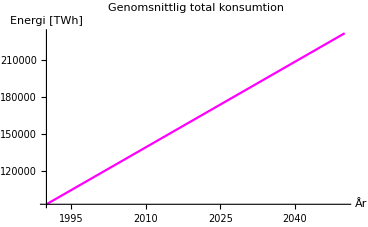
1. Enligt grafen nedan världens energikonsumtion år 2050 är cirka 230 000 TWh. Funktionen totaltfunktion[2050] ger värdet 231 747 TWh.  
-Graphics-

2. Enligt grafen nedan går det att uppskatta att olja som energikälla kan ersättas av förnybara källor mot slutet av år 2031, eftersom solenergi passerar konsumtionen av energi från olja då. År 2036 passerar även energin från vindkraft konsumtionen av energi från olja.

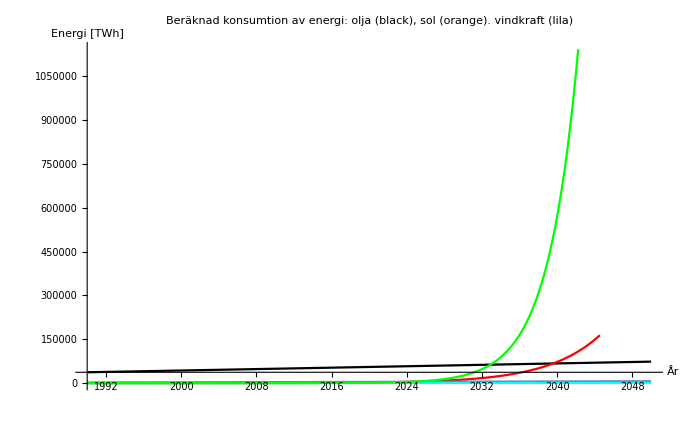

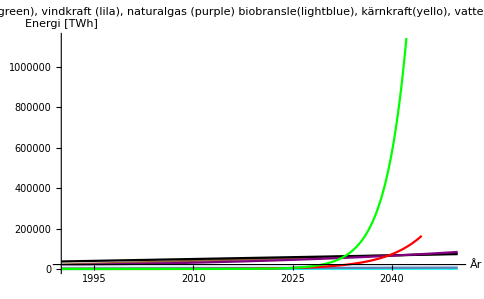
3. Världens energikomsumtion kommer att bli CO2 fri när antal energikomsumtion är lika med energi konsumtion från vatten, sol, krändkraft och vind. Med hjälp av grafen nedan kan man analysera att under året 2036 sol och vindkraft stiger exponentiell. Dessutom formeln totaltfunktion[2036] ger  199 339 TWh och formeln: vattenfunktion[2036]+vindfunktion[2036]+solfunktion[2036]+karnkraftfunktion[2036]
ger 208 512TWh. Detta visar att cirka 2036 alla enegikonsumtion kommer att bli CO2 fria. 

-Graphics-

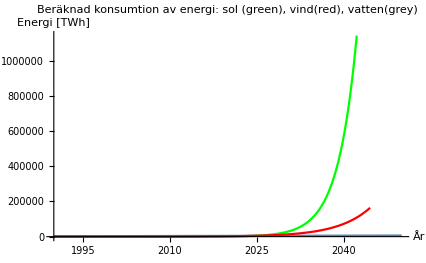
4. Enligt grafen nedan kan man analysera att energikonsumtion från sol, vatten och vindkraft kommer att bli storst inom förnybara energi.
-Graphics-




5. Valda model hade data till 2017. Dessa data hjälpte oss att göra regressionsanalys och rita en linje med bästa passform med användning av FindFit[ ], exempel: {akol,bkol}={a,b}/.FindFit[kol,{a(t-1990)+b},{a,b},t]  . Efter FindFit[ ] har vi skapade en funktion, exempel: kolfunktion[t_]:=akol(t-1990)+bkol , som extrapolerade givna data till året 2050 eller vilka som helst år man ger värdet till.

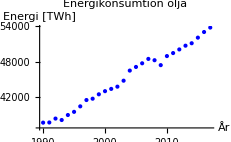
6. Beroende av data tabellen som vi har fått kan man säga att  förutsägelser är rimliga. Brukar statistiska modeller är mer noggrann om det finns mer data att göra regressionanalysis med. Data var från 1990 till 2017 och om vi har haft data till 2020 kunde modellen bli lite mer exakt. Men om man extrapolerar data till 2030 är det mer noggrannt än 2050.


7.   Det finns två typer av felkällor: data och extrapolering av grafer. Exempel på den första kan man se på grafen av olja komsumtion. Det visar att olja konsumtion minskade drastiskt under året 2009. Detta kan kallas för avvikelser av data från deras natural mönster, men användning av linje med bästa passform hjälper att fortsätta med korrelationen. 
-Graphics-

För den andra kan man se att solenegi grafen nedan är en exponentialla graf. Om man skulle räkna solkonsumtion värde under året 2050 är modellen inte rimligt.

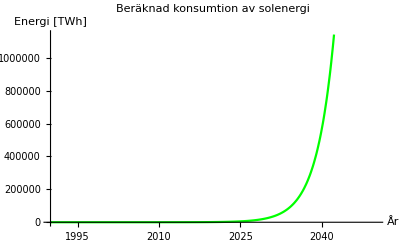

## Visualisera data

### 1. Graf total energikonsumtion

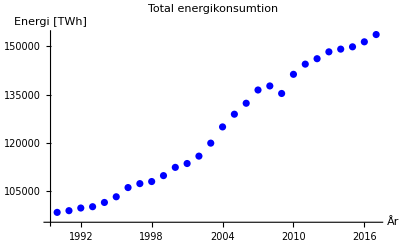

```mathematica
datatotalt=ListPlot[totalt,AxesLabel->{"År","Energi [TWh]"},
PlotLabel->"Total energikonsumtion",PlotStyle->{Blue}]
```

```mathematica
{atotalt,btotalt}={a,b}/.FindFit[totalt,{a(t-1990)+b},{a,b},t]
```

{2314.87,92855.}

```mathematica
totaltfunktion[t_]:=atotalt(t-1990)+btotalt
```

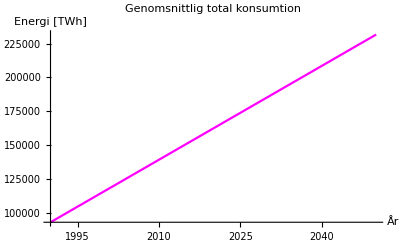

```mathematica
genomsnitttotalt=Plot[totaltfunktion[t],{t,1990,2050},AxesLabel->{"År","Energi [TWh]"},
PlotStyle->{Magenta},PlotLabel->"Genomsnittlig total konsumtion"]
```

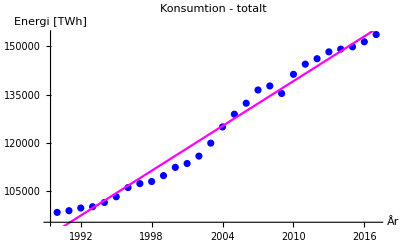

```mathematica
Show[datatotalt,genomsnitttotalt,PlotLabel->"Konsumtion - totalt"]
```

```mathematica
totaltfunktion[2050]
```

231747.

Världens energikonsumtion 2050 uppskattas vara 231747 TWh.

### 2. Graf energikonsumtion olja & förnybara källor

Olja:

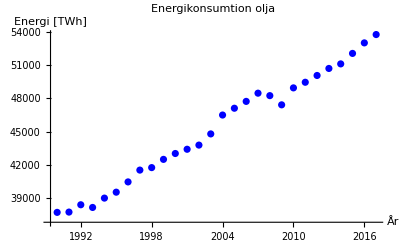

```mathematica
dataolja=ListPlot[olja,AxesLabel->{"År","Energi [TWh]"},
PlotLabel->"Energikonsumtion olja",PlotStyle->{Blue}]
```

```mathematica
{aolja,bolja}={a,b}/.FindFit[olja,{a(t-1990)+b},{a,b},t]
```

{606.174,37053.3}

```mathematica
oljafunktion[t_]:=aolja(t-1990)+bolja
```

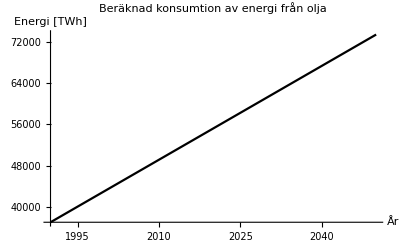

```mathematica
beraknadolja=Plot[oljafunktion[t],{t,1990,2050},AxesLabel->{"År","Energi [TWh]"},
PlotStyle->{Black},PlotLabel->"Beräknad konsumtion av energi från olja"]
```

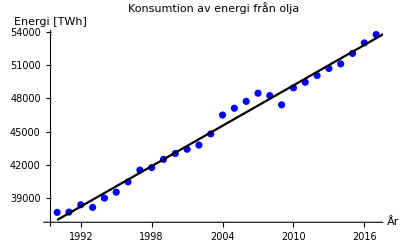

```mathematica
Show[dataolja,beraknadolja,PlotLabel->"Konsumtion av energi från olja"]
```

```mathematica
oljafunktion[2050]
```

73423.7

Världens konsumtion av energi från olja 2050 uppskattas vara 73423.7 TWh.

Vattenkraft:

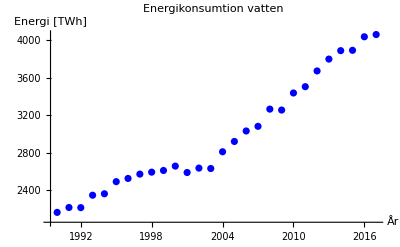

```mathematica
datavatten=ListPlot[vatten,AxesLabel->{"År","Energi [TWh]"},
PlotLabel->"Energikonsumtion vatten",PlotStyle->{Blue}]
```

```mathematica
{avatten,bvatten}={a,b}/.FindFit[vatten,{a(t-1990)+b},{a,b},t]
```

{71.3453,2008.72}

```mathematica
vattenfunktion[t_]:=avatten(t-1990)+bvatten
```

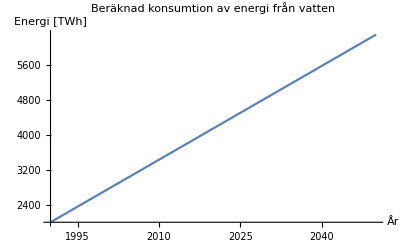

```mathematica
beraknadvatten=Plot[vattenfunktion[t],{t,1990,2050},AxesLabel->{"År","Energi [TWh]"},
PlotStyle->{Grey},PlotLabel->"Beräknad konsumtion av energi från vatten"]
```

Vindkraft:

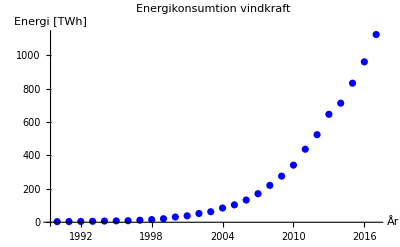

```mathematica
datavind=ListPlot[vind,AxesLabel->{"År","Energi [TWh]"},
PlotLabel->"Energikonsumtion vindkraft",PlotStyle->{Blue}]
```

```mathematica
{avind,bvind}={a,b}/.FindFit[vind,{a Exp[b(t-1990)]},{a,b},t]
```

{9.25548,0.179304}

```mathematica
vindfunktion[t_]:=avind Exp[bvind(t-1990)]
```

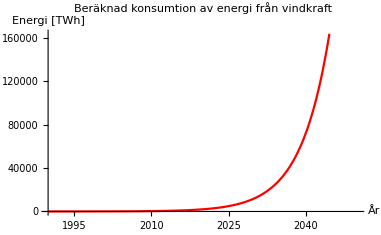

```mathematica
beraknadvind=Plot[vindfunktion[t],{t,1990,2050},AxesLabel->{"År","Energi [TWh]"},
PlotStyle->{Red},PlotLabel->"Beräknad konsumtion av energi från vindkraft"]
```

Solenergi:

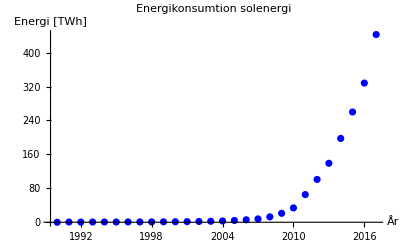

```mathematica
datasol=ListPlot[sol,AxesLabel->{"År","Energi [TWh]"},
PlotLabel->"Energikonsumtion solenergi",PlotStyle->{Blue}]
```

```mathematica
{asol,bsol}={a,b}/.FindFit[sol,{a Exp[b(t-1990)]},{a,b},t]
```

{0.104136,0.310299}

```mathematica
solfunktion[t_]:=asol Exp[bsol(t-1990)]
```

```mathematica
beraknadsol=Plot[solfunktion[t],{t,1990,2050},AxesLabel->{"År","Energi [TWh]"},
PlotStyle->{Green},PlotLabel->"Beräknad konsumtion av solenergi"]
```

-Graphics-

Andra förnybara energikällor:

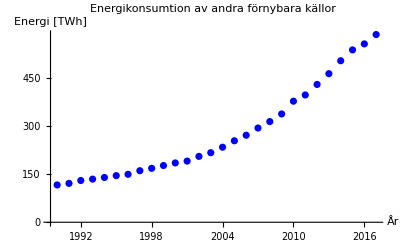

```mathematica
dataandrafornybara=ListPlot[andrafornybara,AxesLabel->{"År","Energi [TWh]"},
PlotLabel->"Energikonsumtion av andra förnybara källor",PlotStyle->{Blue}]
```

```mathematica
{aandrafornybara,bandrafornybara}={a,b}/.FindFit[andrafornybara,{a(t-1990)+b},{a,b},t]
```

{17.1558,47.2089}

```mathematica
andrafornybarafunktion[t_]:=aandrafornybara(t-1990)+bandrafornybara
```

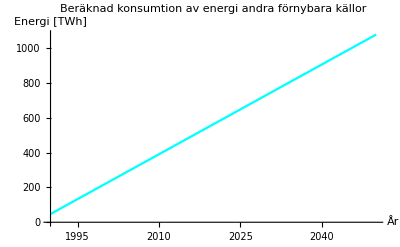

```mathematica
beraknadandrafornybara=Plot[andrafornybarafunktion[t],{t,1990,2050},AxesLabel->{"År","Energi [TWh]"},
PlotStyle->{Cyan},PlotLabel->"Beräknad konsumtion av energi andra förnybara källor"]
```

Jämförelse med alla förnybara energikällor och kol:

```mathematica
Show[beraknadolja,beraknadvind,beraknadvatten, beraknadandrafornybara,beraknadsol,PlotLabel->"Beräknad konsumtion av energi: olja (black), sol (orange). vindkraft (lila)", PlotRange->Automatic]
```

-Graphics-

### 3. Graf energikonsumtion kol, naturalgas, biobränsle & kärnkraft

```mathematica
Kolenergi:
```

```mathematica
SetOptions[$FrontEndSession,ShowGroupOpener->True]
```

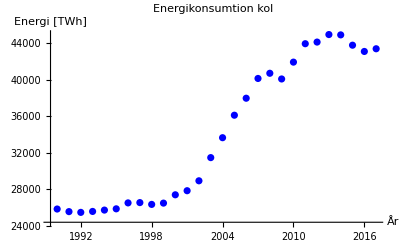

```mathematica
datakol=ListPlot[kol,AxesLabel->{"År","Energi [TWh]"},
PlotLabel->"Energikonsumtion kol",PlotStyle->{Blue}]
```

```mathematica
{akol,bkol}={a,b}/.FindFit[kol,{a(t-1990)+b},{a,b},t]
```

{908.405,21826.1}

```mathematica
kolfunktion[t_]:=akol(t-1990)+bkol
```

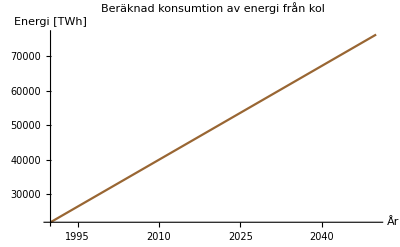

```mathematica
beraknadkol=Plot[kolfunktion[t],{t,1990,2050},AxesLabel->{"År","Energi [TWh]"},
PlotStyle->{Brown},PlotLabel->"Beräknad konsumtion av energi från kol"]
```

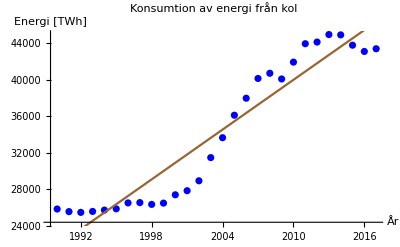

```mathematica
Show[datakol,beraknadkol,PlotLabel->"Konsumtion av energi från kol"]
```

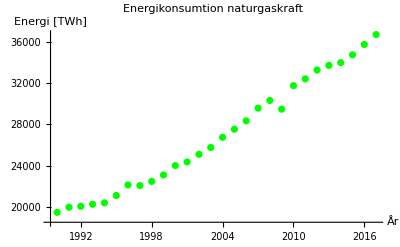

```mathematica
Naturgasenergi:
datanaturgas=ListPlot[naturgas,AxesLabel->{"År","Energi [TWh]"},
PlotLabel->"Energikonsumtion naturgaskraft",PlotStyle->{Green}]
```

```mathematica
{anaturgas,bnaturgas}={a,b}/.FindFit[naturgas,{a Exp[b(t-1990)]},{a,b},t]
```

{18874.3,0.0249077}

```mathematica
naturgasfunktion[t_]:=anaturgas Exp[bnaturgas(t-1990)]
```

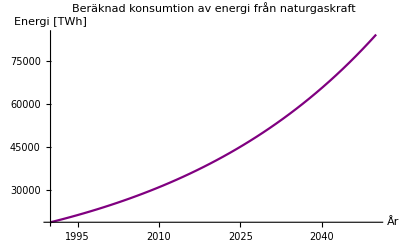

```mathematica
beraknadnaturgas=Plot[naturgasfunktion[t],{t,1990,2050},AxesLabel->{"År","Energi [TWh]"},
PlotStyle->{Purple},PlotLabel->"Beräknad konsumtion av energi från naturgaskraft"]
```

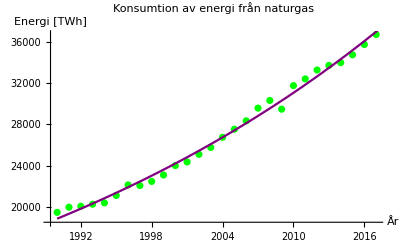

```mathematica
Show[datanaturgas,beraknadnaturgas,PlotLabel->"Konsumtion av energi från naturgas"]
```

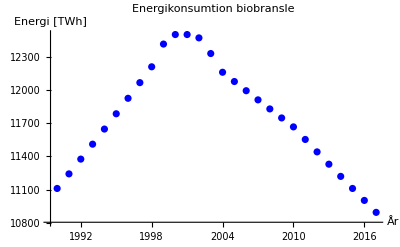

```mathematica
Biobränsleenergi:
databiobransle=ListPlot[biobransle,AxesLabel->{"År","Energi [TWh]"},
PlotLabel->"Energikonsumtion biobransle",PlotStyle->{Blue}]
```

```mathematica
{abiobransle,bbiobransle}={a,b}/.FindFit[biobransle,{a(t-1990)+b},{a,b},t]
```

{-17.7882,11990.9}

```mathematica
biobranslefunktion[t_]:=abiobransle(t-1990)+bbiobransle
```

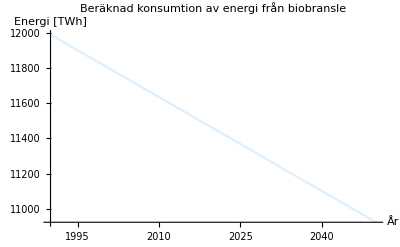

```mathematica
beraknadbiobransle=Plot[biobranslefunktion[t],{t,1990,2050},AxesLabel->{"År","Energi [TWh]"},
PlotStyle->{LightBlue},PlotLabel->"Beräknad konsumtion av energi från biobransle"]
```

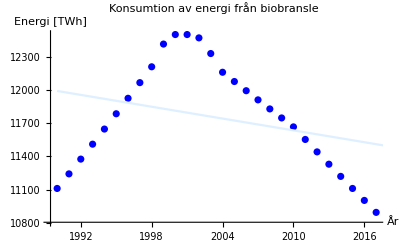

```mathematica
Show[databiobransle,beraknadbiobransle,PlotLabel->"Konsumtion av energi från biobransle"]
```

```mathematica
Kärnkraftsenergi:
```

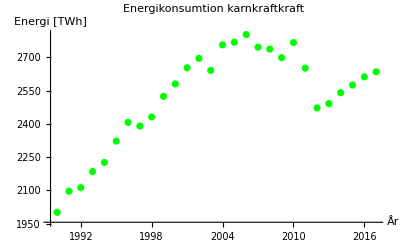

```mathematica
datakarnkraft=ListPlot[karnkraft,AxesLabel->{"År","Energi [TWh]"},
PlotLabel->"Energikonsumtion karnkraftkraft",PlotStyle->{Green}]
```

```mathematica
{akarnkraft,bkarnkraft}={a,b}/.FindFit[karnkraft,{a Exp[b(t-1990)]},{a,b},t]
```

{2276.,0.00738811}

```mathematica
karnkraftfunktion[t_]:=akarnkraft Exp[bkarnkraft(t-1990)]
```

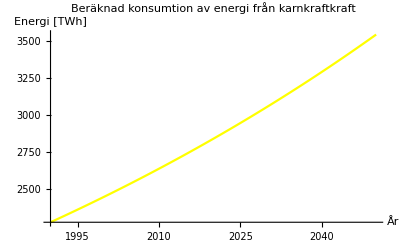

```mathematica
beraknadkarnkraft=Plot[karnkraftfunktion[t],{t,1990,2050},AxesLabel->{"År","Energi [TWh]"},
PlotStyle->{Yellow,},PlotLabel->"Beräknad konsumtion av energi från karnkraftkraft"]
```

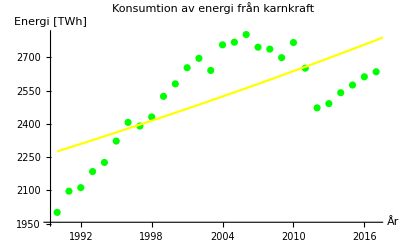

```mathematica
Show[datakarnkraft,beraknadkarnkraft,PlotLabel->"Konsumtion av energi från karnkraft"]
```

## Analysera data

```mathematica
Show[beraknadkol, beraknadolja, beraknadnaturgas, beraknadkarnkraft, beraknadbiobransle, beraknadandrafornybara, beraknadvatten, beraknadvind, beraknadsol, PlotLabel->"Beräknad konsumtion av energi: 
			olja (black), sol (green), vindkraft (lila), naturalgas (purple)
			biobransle(lightblue), kärnkraft(yello), vattenkraft(grey)
			vindkraft(red), Andra förnybara källor(cyan)", PlotRange->Automatic]
```

-Graphics-

Engerikonsumtion 2036:

```mathematica
totaltfunktion[2036]
```

199339.

```mathematica
vattenfunktion[2036]+vindfunktion[2036]+solfunktion[2036]+karnkraftfunktion[2036]
```

208512.

Viktigast förnybara energi 2050:

```mathematica
Show[beraknadsol, beraknadvatten, beraknadvind, PlotLabel->"Beräknad konsumtion av energi: sol (green), vind(red), vatten(grey)", PlotRange-> Automatic]
```

-Graphics-

## Referenser

För den första uppgift Fadil visade gruppen hur listor fungerar och hur man kopplar ihop data med list funtion. 

För den andra uppgift Fadil hjälpte att visa hur man gör regressionanalysis av data med hjälp av FindFit [ ] funktion. Dessutom visade hur man skulle bestämma att grafen kommer att bli linear eller exponentiell.